```mathematica
Clear["Global`*"]
```

```mathematica
blah[wvar_] := Module[{w=wvar,vperp,B0,Ne,Neh,me,kT,EPS0,wp,wph,wc,clight,L,R,P,S,theta,,A,B,CC,n2,tmp1,n,m,kmag,kpar,kperp,Jm,Jmp1,Jmm1,G1,G2,vpar,Di,ki},
B0 = 2.4864*10^-7;
Ne = 5*10^6;
Neh  = .1*10^6;
me = 9.10938188*10^-31;
kT = 5000*1.60217646*10^-19;
q = -1.60217646*10^-19;
F[vperp_,vpar_] := Neh*(me/(2*Pi*kT))^(3/2)*Exp[-me*(vperp^2+vpar^2)/2/kT];
EPS0 = 8.854187817*10^-12;
wp = Sqrt[Ne*q^2/me/EPS0];
wph = Sqrt[Neh*q^2/me/EPS0];
wc = B0*q/me;
clight=299792458;
L = 1-wp^2/(w*(w-wc));
R = 1-wp^2/(w*(w+wc));
P = 1-(wp/w)^2;
S = .5*(R+L);
theta = 60*2*Pi/360;
A = S*Sin[theta]^2+P*Cos[theta]^2;
B = R*L*Sin[theta]^2+P*S*(1+Cos[theta]^2);
CC = R*L*P;
n2=Roots[A*x^2-B*x+CC==0,x];
tmp1={ToRules[n2]};
n = Sqrt[Max[x/.tmp1]];
m=0;
kmag = n*w/(clight);
kpar = kmag*Cos[theta];
kperp = kmag*Sin[theta];
Jm[vperpvar_] := BesselJ[m,kperp*vperpvar/wc];
Jmp1[vperpvar_] := BesselJ[m+1,kperp*vperpvar/wc];
Jmm1[vperpvar_] := BesselJ[m-1,kperp*vperpvar/wc];
tmp2:=D[F[vperpvar,vparvar],vperpvar] - kpar/w*(vpar*D[F[vperpvar,vparvar],vperpvar]-vperpvar*D[F[vperpvar,vparvar],vparvar]);
G1[vperpvar_,vparvar_] = tmp2;
tmp3 :=Jm[vperpvar]*(D[F[vperpvar,vparvar],vparvar]);
G2[vperpvar_,vparvar_] = tmp3;
vpar = (w-m*wc)/kpar;
integrand[vperp_] :=(G1[vperp,vpar]*((P-n^2*Sin[theta]^2)*(2*(L-n^2)*vperp*Jmp1[vperp]^2+2*vperp*(R-n^2)*Jmm1[vperp]^2+n^2*Sin[theta]^2*vperp*(Jmp1[vperp]-Jmm1[vperp])^2)-n^2*Cos[theta]*Sin[theta]*(2*vpar*Jm[vperp]*(Jmp1[vperp]*(R-n^2)+Jmm1[vperp]*(L-n^2))+n^2*Cos[theta]*Sin[theta]*vperp*(Jmp1[vperp]-Jmm1[vperp])^2))+G2[vperp,vpar]*((4*vpar*Jm[vperp]*((L-n^2)*(R-n^2)+n^2*Sin[theta]^2*(S-n^2))-2*n^2*Cos[theta]*Sin[theta]*((R-n^2)*vperp*Jmm1[vperp]+(L-n^2)*vperp*Jmp1[vperp]))));
Di = (-2*Pi^2*wph^2/Neh/w/Abs[kpar])*NIntegrate[vperp*integrand[vperp],{vperp,0,3*10^8}];ki = (-w/(clight))*(1/2)*(1/(4*n*(2*A*n^2-B)))*Di;
ki
]
```

```mathematica
B0 = 2.4864*10^-7;
me = 9.10938188*10^-31;
wc = B0*q/me;
blah[.7*Abs[wc]]
```

0.+4.97097×10^6 ⅈ

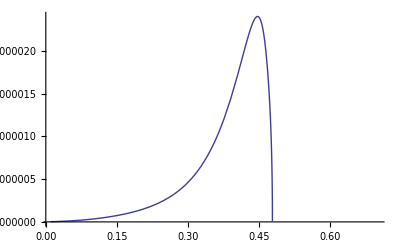

```mathematica
Plot[blah[wf*Abs[wc]],{wf,.01,.7}]
```